```mathematica
ClearAll["Global`*"]
f[x_] := a(x-b)
g[x_]:= ⅇ^(-x^2/σ^2)
```

```mathematica
h=Integrate[f[t] g[x-t], {t, -∞, ∞}][[1]]
```

(a √π (-b+x))/(√(1/σ^2))

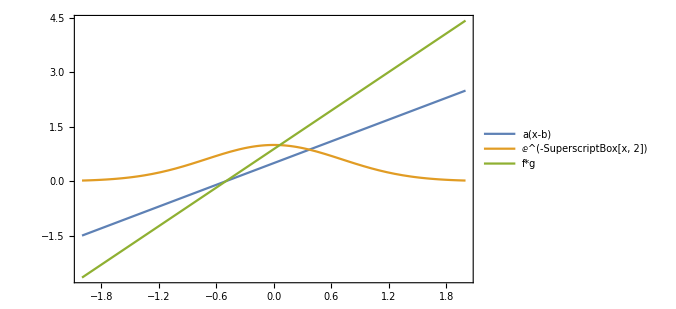

```mathematica
Plot[Evaluate[{f[x], g[x], h} /.{a -> 1, b-> -0.5, σ->1}], {x, -2, 2}, Frame->True, PlotLegends->{"a(x-b)", "ⅇ^(-SuperscriptBox[x, 2])", "f*g"}, ImageSize->500]
```